```mathematica
SetDirectory[NotebookDirectory[]];
table=Import["data.xlsx"][[1]];
```

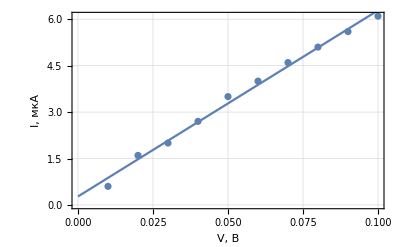

R_ш=(16633.500.) Ω

```mathematica
darkReverse=table[[4;;13,1;;2]];
fitDarkReverse=LinearModelFit[darkReverse,x,x];
eqDarkReverse=fitDarkReverse["BestFit"];
plot1=Show[ListPlot[darkReverse,PlotTheme->"Detailed",FrameLabel->{"V, В", "I, мкА"}],Plot[eqDarkReverse,{x,0,darkReverse[[Length[darkReverse],1]]}]]
parDarkReverse=Transpose[Prepend[Transpose[Prepend[fitDarkReverse["ParameterTableEntries"],{"Estimate","Standard Error","t-Statistic","P-Value"}]],{"","1","x"}]];
k=Quantity[Around[fitDarkReverse["BestFitParameters"][[2]],fitDarkReverse["ParameterErrors"][[2]]],"Microamperes"]/Quantity[1,"Volts"];
Rsh=UnitSimplify[ScientificForm[1/k]];
Print["R_(:0448)=",Rsh]
```

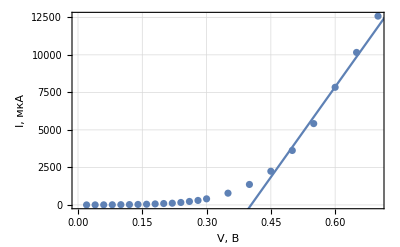

R_п=(24.91.6) Ω

```mathematica
darkDirectSimple=table[[4;;26,4;;5]];
fitDarkDirectSimple=LinearModelFit[darkDirectSimple[[18;;22,All]],x,x];
eqDarkDirectSimple=fitDarkDirectSimple["BestFit"];
parDarkDirectSimple=Transpose[Prepend[Transpose[Prepend[fitDarkDirectSimple["ParameterTableEntries"],{"Estimate","Standard Error","t-Statistic","P-Value"}]],{"","1","x"}]];
plot2=Show[ListPlot[darkDirectSimple,PlotTheme->"Detailed",FrameLabel->{"V, В", "I, мкА"}],Plot[eqDarkDirectSimple,{x,0,1}]]
kp=Quantity[Around[fitDarkDirectSimple["BestFitParameters"][[2]],fitDarkDirectSimple["ParameterErrors"][[2]]],"Microamperes"]/Quantity[1,"Volts"];
Rp=UnitSimplify[ScientificForm[1/kp]];
Print["R_(:043f)=",Rp]
```

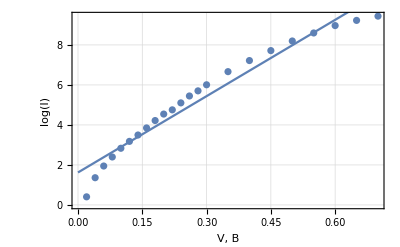

I_s=(5.11.1) µA

A=(3.150.15) /µA

```mathematica
darkDirect=Transpose[{table[[4;;26,4]],Log[table[[4;;26,5]]]}];
fitDarkDirect=LinearModelFit[darkDirect,x,x];
eqDarkDirect=fitDarkDirect["BestFit"];
parDarkDirect=Transpose[Prepend[Transpose[Prepend[fitDarkDirect["ParameterTableEntries"],{"Estimate","Standard Error","t-Statistic","P-Value"}]],{"","1","x"}]];
plot3=Show[ListPlot[darkDirect,PlotTheme->"Detailed",FrameLabel->{"V, В", "log(I)"}],Plot[eqDarkDirect,{x,0,1}]]
Is=Quantity[Exp[Around[fitDarkDirect["BestFitParameters"][[1]],fitDarkDirect["ParameterErrors"][[1]]]],"Microamperes"];
Print["I_s=",Is]
slope=Quantity[Around[fitDarkDirect["BestFitParameters"][[2]],fitDarkDirect["ParameterErrors"][[2]]],"Microamperes"/"Volts"];
a=UnitSimplify[1/(Quantity[0.025,"Volts"]slope)];
Print["A=",a]
```

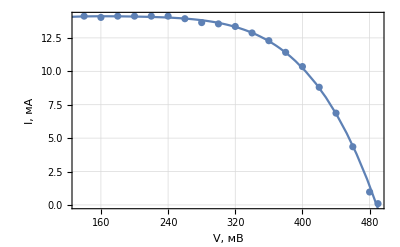

I_(к . з .)=14.1057 µA

U_(x . x .)=488.365 mV

I_н=11.3773 mA

U_н=380.446 mV

R_опт=33.4389 mV/mA

P=4.32847 mW

```mathematica
light=table[[4;;22,8;;9]];
fit=Fit[light,{1,x,x^2,x^3,x^4},x];
plot4=Show[ListPlot[light,PlotTheme->"Detailed",FrameLabel->{"V, мВ", "I, мА"}],Plot[fit,{x,0,600}]]
Ikz=Quantity[fit/.x->Min[light[[All,1]]],"Microamperes"];
Uxx=Quantity[x/.Solve[0==fit,x][[4,1]],"Millivolts"];
Print["I_(:043a . :0437 .)=",Ikz]
Print["U_(x . x .)=",Uxx]
dif=D[fit,x];
un=Quantity[N[x/.Solve[dif==-0.05,x][[3,1]]],"Millivolts"];
in=Quantity[fit/.x->QuantityMagnitude[un],"Milliamperes"];
Rotp=un/in;
Print["I_(:043d)=",in]
Print["U_(:043d)=",un]
Print["R_(:043e:043f:0442)=",Rotp]
ζ=(in*un)/(Ikz*Uxx);
pow=UnitConvert[UnitSimplify[ζ*Uxx*Ikz],"Milliwatts"];
Print["P=",pow]
```

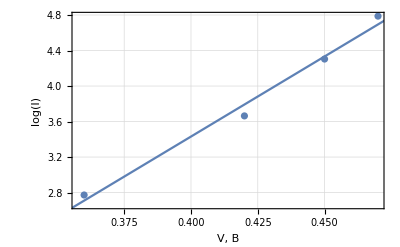

I_s=(0.0230.014) µA

A=(3.150.15) /µA

```mathematica
filters=Transpose[{table[[3;;6,16]],Log[table[[3;;6,17]]]}];
filtersFit=LinearModelFit[filters,x,x];
filtersFitEq=filtersFit["BestFit"];
filtersFitParTab=Transpose[Prepend[Transpose[Prepend[filtersFit["ParameterTableEntries"],{"Estimate","Standard Error","t-Statistic","P-Value"}]],{"","1","x"}]];
plot5=Show[ListPlot[filters,PlotTheme->"Detailed",FrameLabel->{"V, В", "log(I)"}],Plot[filtersFitEq,{x,0,0.5}]]
Isf=Quantity[Exp[Around[filtersFit["BestFitParameters"][[1]],filtersFit["ParameterErrors"][[1]]]],"Microamperes"];
Print["I_s=",Isf]
slopef=Quantity[Around[filtersFit["BestFitParameters"][[2]],filtersFit["ParameterErrors"][[2]]],"Microamperes"/"Volts"];
af=UnitSimplify[1/(Quantity[0.025,"Volts"]slope)];
Print["A=",af]
```

```mathematica
(*Export all*)
Export["plot1.png",plot1,ImageResolution->500];
Export["plot2.png",plot2,ImageResolution->500];
Export["plot3.png",plot3,ImageResolution->500];
Export["plot4.png",plot4,ImageResolution->500];
Export["plot5.png",plot5,ImageResolution->500];
Export["er1.xlsx",parDarkReverse];
Export["er2.xlsx",parDarkDirectSimple];
Export["er3.xlsx",parDarkDirect];
Export["er5.xlsx",filtersFitParTab];
```